```mathematica
s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0.,30.}},<>]}}

```mathematica
xf=Fourier[Table[y[x]/.s,{x,0,30}]]
```

{{1.05156+0. ⅈ},{0.359584+0.215492 ⅈ},{0.282909+0.148899 ⅈ},{0.275574+0.115438 ⅈ},{0.313425+0.120866 ⅈ},{0.204257+0.456288 ⅈ},{0.106024+0.179826 ⅈ},{0.111571+0.131106 ⅈ},{0.118121+0.112616 ⅈ},{0.119967+0.118486 ⅈ},{0.0215331+0.0947526 ⅈ},{0.0659159+0.0585504 ⅈ},{0.0710583+0.042934 ⅈ},{0.0746427+0.0341113 ⅈ},{0.0700368+0.0291543 ⅈ},{0.063484+0.00192355 ⅈ},{0.063484-0.00192355 ⅈ},{0.0700368-0.0291543 ⅈ},{0.0746427-0.0341113 ⅈ},{0.0710583-0.042934 ⅈ},{0.0659159-0.0585504 ⅈ},{0.0215331-0.0947526 ⅈ},{0.119967-0.118486 ⅈ},{0.118121-0.112616 ⅈ},{0.111571-0.131106 ⅈ},{0.106024-0.179826 ⅈ},{0.204257-0.456288 ⅈ},{0.313425-0.120866 ⅈ},{0.275574-0.115438 ⅈ},{0.282909-0.148899 ⅈ},{0.359584-0.215492 ⅈ}}

```mathematica
Re[xf]
```

{{1.05156},{0.359584},{0.282909},{0.275574},{0.313425},{0.204257},{0.106024},{0.111571},{0.118121},{0.119967},{0.0215331},{0.0659159},{0.0710583},{0.0746427},{0.0700368},{0.063484},{0.063484},{0.0700368},{0.0746427},{0.0710583},{0.0659159},{0.0215331},{0.119967},{0.118121},{0.111571},{0.106024},{0.204257},{0.313425},{0.275574},{0.282909},{0.359584}}

```mathematica
s2=NDSolve[{D[u[t,x],t]==D[u[t,x],x,x],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u,{t,0,5},{x,0,5}]
```

{{u→InterpolatingFunction[{{0.,5.},{0.,5.}},<>]}}

```mathematica
xf2=Re[
Fourier[
Table[
u[t,x]/.s2,{t,0,5},{x,0,5}
]
]
]
```

{{{0.381283},{-0.0647287},{-0.0295887},{-0.0169171},{-0.0295887},{-0.0647287}},{{-0.312006},{-0.212858},{-0.0958036},{0.018078},{0.146074},{0.180671}},{{0.0801804},{0.0110964},{-0.0122825},{-0.00661812},{-0.00213653},{0.0532996}},{{0.0823693},{0.03252},{-0.00626255},{-0.00600259},{-0.00626255},{0.03252}},{{0.0801804},{0.0532996},{-0.00213653},{-0.00661812},{-0.0122825},{0.0110964}},{{-0.312006},{0.180671},{0.146074},{0.018078},{-0.0958036},{-0.212858}}}

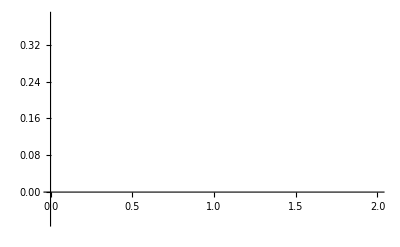

```mathematica
xf2p1=ListLinePlot[xf2[[1]],Color->Red];
xf2p2=ListLinePlot[xf2[[2]]];
xf2p3=ListLinePlot[xf2[[3]]];
Show[xf2p1,xf2p2,xf2p3]
```